## Generalized Model Analysis of the SH0ES Measurement of H_0. Search for a transition is implemented. For different generalized parameters, the parameter ‘col’ needs to be changed and the table qpar1. The rest may even remain as they are (the range of the final plot may also need to be changed).

## Setting the directory

```mathematica
SetDirectory[NotebookDirectory[]];  
Needs["ErrorBarPlots`"];
Needs["ErrorBarLogPlots`"]
Off[General::"obspkg",General::luc,NIntegrate::"inumr",NIntegrate::ncvb,CompiledFunction::cflist,ListInterpolation::inhr,FindMinimum::lstol];
```

## Matrix of Measurements Y- Matrix of Parameters q - Design Matrix L- Error Matrix C

```mathematica
cdata=Import[".\\data\\allc_shoes_ceph_topantheonwt6.0_112221.fits","RawData"];
ydata=Import[".\\data\\ally_shoes_ceph_topantheonwt6.0_112221.fits","RawData"] [[1]]//Normal;
ldata=Import[".\\data\\alll_shoes_ceph_topantheonwt6.0_112221.fits","RawData"]//Normal;
distall=Import[".\\data\\distall.txt","Table"];
dof=3446;
NN=3493;
MM=48;
maxdist=60; (* this is the maximum distance considered in do loop in Mpc that distinguishes nearby and distant objects/constraints in Y.  *)
mindist=8; (* this is the minimum distance considered in do loop in Mpc that distinguishes nearby and distant objects/constraints in Y. For MB the mindist should be at least 7 because the minimum distance of the SnIa in the Y vector is 6.7Mpc (this is in a Cepheid host). Thus for smaller distances there are no SnIa and the sigma matrix is singular. *)
step=2; (* this is the distance step considered in do loop  *)

col=47-4; (* this column corresponds to the parameter to be split (eg for bW period luminosity slope we have col=42 *)
qpar1={μ67,μ385,μ354,μ356,μ738,μ294,μ228,μ163,μ193,μ201,μ272,μ354,μ266,μ425,μ244,μ24,μ208,μ344,μ151,μ190,μ293,μ164,μ319,μ198,μ421,μ463,μ280,μ207,μ449,μ303,μ310,μ128,μ468,μ344,μ466,μ605,μ294,ΔμΝ4258,MW,ΔμLMC,μM31,bW,MBs,MBl,ZW,X,ΔZp,p5ogh0}; (* introduce here the names of the two new parameters that replace the previous parameter *)
```

## The inverse distance ladder constraint

```mathematica
(* The inverse distance ladder constraint on Subscript[M, B] is  Subscript[M, B]=-19.401 ± 0.027*)
```

```mathematica
Yno=ydata;
Y=Insert[Yno,-19.401,3216](* Adding one more constraint to the Y data-vector: after entry 3215 which corresponds to the 8th constraintwe add the value -19.401*);

distno=distall[[All,1]];
dist1=Insert[distno,500,3216](* Adding the distance of constraint *);

Lins=Table[If[i==43,1.,0.],{i,1,47}](*we construct a line with all entries set to zero except the entry at column 43 (corresponding to the parameter MB)  sets to one *);

trLno=ldata[[1]]//Normal;
Lno=Transpose[trLno]; 
L=Insert[Lno,Lins,3216](* Adding one more line to the L matrix: after line 3215 which corresponds to the 8th constraint we add the line Lins*);
MatrixForm[L];
trL=Transpose[L];

Cins1=Table[0.*i,{i,1,3492}](*we construct a line with all entries set to zero *);
Cins2=Table[If[i==3216,0.000729,0.],{i,1,3493}](*we construct a line with all entries set to zero except the entry at column 3216 (corresponding to the parameter MB) sets to 0.027^2=0.00729*);
```

```mathematica
Callno=cdata[[1]]//Normal; (* Covariance matrix*)
Call1=Insert[Callno,Cins1,3216](* Adding one more line to the C matrix: after line 3215 which corresponds to the 8th constraint we add the line Cins1*);

trCall1=Transpose[Call1];
trCall2=Insert[trCall1,Cins2,3216](* Adding one more line to the transpose of C matrix: after line 3215 which corresponds to the 8th constraint we add the line Cins2*);
Call=Transpose[trCall2](* This is the new Covariance matrix*);
InvCall=Inverse[Call];
it=InvCall.Call//Chop;
zerot=it-IdentityMatrix[Length[it]]//Chop;
zerot[[1]];  (* test the inversion of Call due to the mathematica complaints. These are due to the parameter X introduced arbitrarily in the SH0ES data analysis and not shown in https://arxiv.org/pdf/2112.04510.pdf  (Riess21). This leads to Call with a column and raw that are 0 except of the diagonal point which is 10^-9. This raw and column of Call creates the complaints but the end inversion is fine. *)
```

## Search for a transition (M_B) - Results - Figure 12

```mathematica
percol1=L[[All,col]]//Normal; (* construct two columns from the Subscript[M, B] column of L with nearby and distant objects *)
```

Distance=8---------------

H_0=70.5034±0.699083

MBs=-19.4032±0.1023

MBl=-19.3305±0.0198435

σ-distance = 0.697645

Mw=-5.92041±0.01671

Δbw=-0.0251876±0.0145742

Zw=-0.221835±0.0452831

χ_min^2 = 3566.28

χ_red^2 = 1.0349

AIC = 3662.28

ΔAIC = 1.49703

BIC = 3957.88

ΔBIC = 7.65554

Distance=10---------------

H_0=70.5034±0.699083

MBs=-19.4032±0.1023

MBl=-19.3305±0.0198435

σ-distance = 0.697645

Mw=-5.92041±0.01671

Δbw=-0.0251876±0.0145742

Zw=-0.221835±0.0452831

χ_min^2 = 3566.28

χ_red^2 = 1.0349

AIC = 3662.28

ΔAIC = 1.49703

BIC = 3957.88

ΔBIC = 7.65554

Distance=12---------------

H_0=70.5034±0.699083

MBs=-19.4032±0.1023

MBl=-19.3305±0.0198435

σ-distance = 0.697645

Mw=-5.92041±0.01671

Δbw=-0.0251876±0.0145742

Zw=-0.221835±0.0452831

χ_min^2 = 3566.28

χ_red^2 = 1.0349

AIC = 3662.28

ΔAIC = 1.49703

BIC = 3957.88

ΔBIC = 7.65554

Distance=14---------------

H_0=70.5104±0.700124

MBs=-19.3966±0.0928261

MBl=-19.3303±0.0198768

σ-distance = 0.6984

Mw=-5.9204±0.0167088

Δbw=-0.0252713±0.0145703

Zw=-0.22123±0.0452391

χ_min^2 = 3566.27

χ_red^2 = 1.0349

AIC = 3662.27

ΔAIC = 1.49314

BIC = 3957.88

ΔBIC = 7.65166

Distance=16---------------

H_0=70.423±0.701299

MBs=-19.3047±0.0764833

MBl=-19.3331±0.0199452

σ-distance = 0.359435

Mw=-5.91899±0.0167273

Δbw=-0.0256463±0.0145656

Zw=-0.219052±0.0452563

χ_min^2 = 3566.64

χ_red^2 = 1.03501

AIC = 3662.64

ΔAIC = 1.86324

BIC = 3958.25

ΔBIC = 8.02176

Distance=18---------------

H_0=70.3607±0.703244

MBs=-19.2792±0.0633637

MBl=-19.3351±0.0200529

σ-distance = 0.841587

Mw=-5.91809±0.0167441

Δbw=-0.0256063±0.0145642

Zw=-0.218288±0.0452366

χ_min^2 = 3566.01

χ_red^2 = 1.03483

AIC = 3662.01

ΔAIC = 1.2315

BIC = 3957.62

ΔBIC = 7.39002

Distance=20---------------

H_0=70.5212±0.71253

MBs=-19.3508±0.0485152

MBl=-19.3299±0.0203451

σ-distance = 0.39678

Mw=-5.92039±0.0167888

Δbw=-0.0256904±0.0145669

Zw=-0.220358±0.0452134

χ_min^2 = 3566.6

χ_red^2 = 1.035

AIC = 3662.6

ΔAIC = 1.82066

BIC = 3958.21

ΔBIC = 7.97918

Distance=22---------------

H_0=70.456±0.728992

MBs=-19.3318±0.0384798

MBl=-19.332±0.0208502

σ-distance = 0.0041498

Mw=-5.91951±0.0169146

Δbw=-0.0255678±0.0145845

Zw=-0.219876±0.0452802

χ_min^2 = 3566.78

χ_red^2 = 1.03505

AIC = 3662.78

ΔAIC = 1.99998

BIC = 3958.39

ΔBIC = 8.1585

Distance=24---------------

H_0=70.6038±0.737147

MBs=-19.351±0.0367554

MBl=-19.3275±0.0210369

σ-distance = 0.554178

Mw=-5.92137±0.0169325

Δbw=-0.0260545±0.0145855

Zw=-0.221046±0.0452394

χ_min^2 = 3566.4

χ_red^2 = 1.03494

AIC = 3662.4

ΔAIC = 1.62477

BIC = 3958.01

ΔBIC = 7.78329

Distance=26---------------

H_0=70.3137±0.748428

MBs=-19.3178±0.0340778

MBl=-19.3364±0.0215017

σ-distance = 0.461444

Mw=-5.91786±0.0169793

Δbw=-0.0249905±0.0146084

Zw=-0.219658±0.045202

χ_min^2 = 3566.52

χ_red^2 = 1.03497

AIC = 3662.52

ΔAIC = 1.73814

BIC = 3958.13

ΔBIC = 7.89666

Distance=28---------------

H_0=70.3398±0.755582

MBs=-19.3214±0.0333187

MBl=-19.3356±0.021718

σ-distance = 0.355162

Mw=-5.91813±0.0170414

Δbw=-0.0251049±0.0146124

Zw=-0.219396±0.0452171

χ_min^2 = 3566.62

χ_red^2 = 1.035

AIC = 3662.62

ΔAIC = 1.84544

BIC = 3958.23

ΔBIC = 8.00395

Distance=30---------------

H_0=69.8385±0.78163

MBs=-19.2924±0.030796

MBl=-19.351±0.0227799

σ-distance = 1.52945

Mw=-5.91239±0.0172011

Δbw=-0.0226759±0.0146668

Zw=-0.219575±0.0452002

χ_min^2 = 3563.98

χ_red^2 = 1.03424

AIC = 3659.98

ΔAIC = -0.796381

BIC = 3955.59

ΔBIC = 5.36214

Distance=32---------------

H_0=69.7613±0.798058

MBs=-19.293±0.0300952

MBl=-19.3534±0.0233301

σ-distance = 1.58603

Mw=-5.91165±0.0172841

Δbw=-0.0223027±0.0146881

Zw=-0.220476±0.0452011

χ_min^2 = 3563.83

χ_red^2 = 1.03419

AIC = 3659.83

ΔAIC = -0.947372

BIC = 3955.44

ΔBIC = 5.21114

Distance=34---------------

H_0=69.7613±0.798058

MBs=-19.293±0.0300952

MBl=-19.3534±0.0233301

σ-distance = 1.58603

Mw=-5.91165±0.0172841

Δbw=-0.0223027±0.0146881

Zw=-0.220476±0.0452011

χ_min^2 = 3563.83

χ_red^2 = 1.03419

AIC = 3659.83

ΔAIC = -0.947372

BIC = 3955.44

ΔBIC = 5.21114

Distance=36---------------

H_0=69.2364±0.826153

MBs=-19.2756±0.029272

MBl=-19.3695±0.0244191

σ-distance = 2.46343

Mw=-5.90558±0.0175008

Δbw=-0.0194243±0.0147538

Zw=-0.219818±0.0451998

χ_min^2 = 3559.98

χ_red^2 = 1.03308

AIC = 3655.98

ΔAIC = -4.79899

BIC = 3951.59

ΔBIC = 1.35952

Distance=38---------------

H_0=69.2364±0.826153

MBs=-19.2756±0.029272

MBl=-19.3695±0.0244191

σ-distance = 2.46343

Mw=-5.90558±0.0175008

Δbw=-0.0194243±0.0147538

Zw=-0.219818±0.0451998

χ_min^2 = 3559.98

χ_red^2 = 1.03308

AIC = 3655.98

ΔAIC = -4.79899

BIC = 3951.59

ΔBIC = 1.35952

Distance=40---------------

H_0=69.1738±0.832838

MBs=-19.2748±0.0291298

MBl=-19.3714±0.0246511

σ-distance = 2.53081

Mw=-5.90495±0.017537

Δbw=-0.0190489±0.0147681

Zw=-0.220311±0.0452001

χ_min^2 = 3559.67

χ_red^2 = 1.03298

AIC = 3655.67

ΔAIC = -5.11304

BIC = 3951.27

ΔBIC = 1.04547

Distance=42---------------

H_0=69.1738±0.832838

MBs=-19.2748±0.0291298

MBl=-19.3714±0.0246511

σ-distance = 2.53081

Mw=-5.90495±0.017537

Δbw=-0.0190489±0.0147681

Zw=-0.220311±0.0452001

χ_min^2 = 3559.67

χ_red^2 = 1.03298

AIC = 3655.67

ΔAIC = -5.11304

BIC = 3951.27

ΔBIC = 1.04547

Distance=44---------------

H_0=69.0722±0.838116

MBs=-19.272±0.0290554

MBl=-19.3746±0.0248737

σ-distance = 2.68359

Mw=-5.90364±0.0175939

Δbw=-0.0185014±0.0147793

Zw=-0.219402±0.0452001

χ_min^2 = 3558.86

χ_red^2 = 1.03275

AIC = 3654.86

ΔAIC = -5.91733

BIC = 3950.47

ΔBIC = 0.241191

Distance=46---------------

H_0=69.1134±0.842043

MBs=-19.2745±0.0290443

MBl=-19.3733±0.0249811

σ-distance = 2.57917

Mw=-5.90405±0.0176239

Δbw=-0.0187579±0.0147817

Zw=-0.218899±0.0452013

χ_min^2 = 3559.51

χ_red^2 = 1.03294

AIC = 3655.51

ΔAIC = -5.27252

BIC = 3951.12

ΔBIC = 0.885991

Distance=48---------------

H_0=68.2019±0.878769

MBs=-19.249±0.0289056

MBl=-19.4019±0.0265716

σ-distance = 3.89503

Mw=-5.89328±0.0179529

Δbw=-0.013215±0.0148999

Zw=-0.217168±0.0452051

χ_min^2 = 3551.34

χ_red^2 = 1.03057

AIC = 3647.34

ΔAIC = -13.4357

BIC = 3942.95

ΔBIC = -7.27721

Distance=50---------------

H_0=68.2019±0.878769

MBs=-19.249±0.0289056

MBl=-19.4019±0.0265716

σ-distance = 3.89503

Mw=-5.89328±0.0179529

Δbw=-0.013215±0.0148999

Zw=-0.217168±0.0452051

χ_min^2 = 3551.34

χ_red^2 = 1.03057

AIC = 3647.34

ΔAIC = -13.4357

BIC = 3942.95

ΔBIC = -7.27721

Distance=52---------------

H_0=68.2019±0.878769

MBs=-19.249±0.0289056

MBl=-19.4019±0.0265716

σ-distance = 3.89503

Mw=-5.89328±0.0179529

Δbw=-0.013215±0.0148999

Zw=-0.217168±0.0452051

χ_min^2 = 3551.34

χ_red^2 = 1.03057

AIC = 3647.34

ΔAIC = -13.4357

BIC = 3942.95

ΔBIC = -7.27721

Distance=54---------------

H_0=68.2019±0.878769

MBs=-19.249±0.0289056

MBl=-19.4019±0.0265716

σ-distance = 3.89503

Mw=-5.89328±0.0179529

Δbw=-0.013215±0.0148999

Zw=-0.217168±0.0452051

χ_min^2 = 3551.34

χ_red^2 = 1.03057

AIC = 3647.34

ΔAIC = -13.4357

BIC = 3942.95

ΔBIC = -7.27721

Distance=56---------------

H_0=68.2019±0.878769

MBs=-19.249±0.0289056

MBl=-19.4019±0.0265716

σ-distance = 3.89503

Mw=-5.89328±0.0179529

Δbw=-0.013215±0.0148999

Zw=-0.217168±0.0452051

χ_min^2 = 3551.34

χ_red^2 = 1.03057

AIC = 3647.34

ΔAIC = -13.4357

BIC = 3942.95

ΔBIC = -7.27721

Distance=58---------------

H_0=68.2019±0.878769

MBs=-19.249±0.0289056

MBl=-19.4019±0.0265716

σ-distance = 3.89503

Mw=-5.89328±0.0179529

Δbw=-0.013215±0.0148999

Zw=-0.217168±0.0452051

χ_min^2 = 3551.34

χ_red^2 = 1.03057

AIC = 3647.34

ΔAIC = -13.4357

BIC = 3942.95

ΔBIC = -7.27721

Distance=60---------------

H_0=68.2019±0.878769

MBs=-19.249±0.0289056

MBl=-19.4019±0.0265716

σ-distance = 3.89503

Mw=-5.89328±0.0179529

Δbw=-0.013215±0.0148999

Zw=-0.217168±0.0452051

χ_min^2 = 3551.34

χ_red^2 = 1.03057

AIC = 3647.34

ΔAIC = -13.4357

BIC = 3942.95

ΔBIC = -7.27721

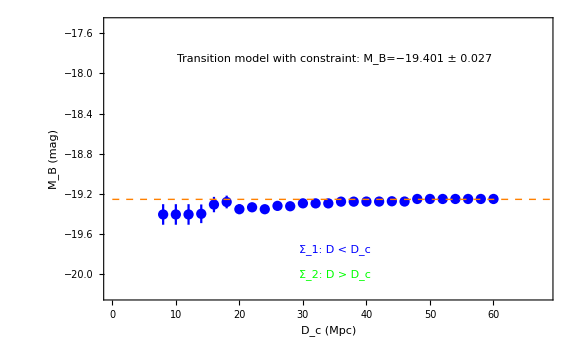
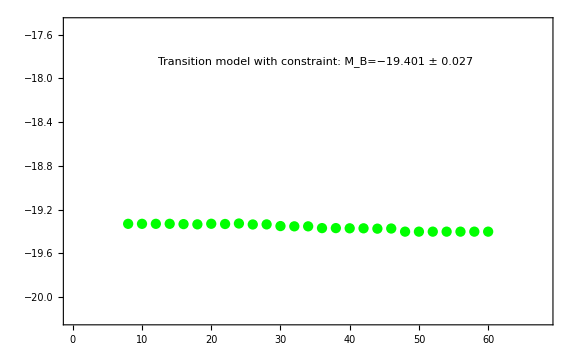
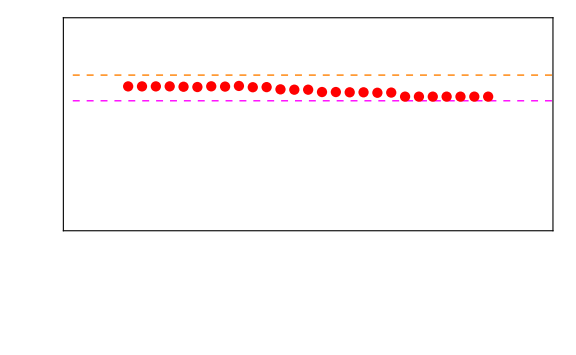

```mathematica
plh0dat={};
plparsdat={};
plparldat={};
plsdist={};
plchi2min={};
plchi2red={};
plaic={};
pldaic={};
plbic={};
pldbic={};
pldchi={};
Do[
percol1s=percol1;
percol1l=percol1;
Do[
If[dist1[[i]]≥ dcrit,percol1s[[i]]=0]; (* in the nearby Subscript[M, B,s] column put 0 in the distant elements ie those that are beyond dcrit *)
If[0<=dist1[[i]]< dcrit,percol1l[[i]]=0] (* in the distant Subscript[M, B,l] column put 0 in the nearby elements ie those that are closer than dcrit. Elements with negative distance are ignored. *)
,{i,1,Length[dist1]}];
trL1=Drop[trL,{col}] ;(* Remove the Mb column of L to replace it with two other columns for the nearby and distant parameters (M Subscript[M, B,s] Bs and Subscript[M, B,l]) *)
trL2=Insert[Insert[trL1,percol1s,col],percol1l,col+1] ;(* Replace with the new columns *)
Lnew=Transpose[trL2]; (* this is the model matrix Lnew for the new model with one new parameter *)
trLnew=trL2 ;(* The system is Y=L qpar. qpar has single column with 47 entries. Entry 45 is useless and does not appear anywhere but we keep it for completeness as it has been included in the fits data but it is not mentioned in Riess 21. *);
sigma=Inverse[trLnew.InvCall.Lnew];
qbf=sigma.(trLnew.InvCall.Y) ;(* These are the best fit parameter values. These formulas are proven in https://people.duke.edu/~hpgavin/SystemID/CourseNotes/linear-least-squres.pdf eq. 11 *);
(* the best fit papameter values with 1 sigma errors for H0 and for the two new parameters *)
h0=10^(qbf[[48]]/5) (* We obtain the correct value of h0 since qbf[[47]]= 5 log Subscript[H, 0]  *);
dqbf48=Sqrt[sigma[[48,48]]];
dh0=Log[10] h0 dqbf48/5 ;
vec=Y-Lnew.qbf;
chi2min=vec.InvCall.vec;
Print["Distance=",dcrit,"---------------"];
Print["H_0=",h0,"±",dh0];
dpars=Sqrt[sigma[[col,col]]];
dparl=Sqrt[sigma[[col+1,col+1]]];
pars=ToString[qpar1[[col]]];
parl=ToString[qpar1[[col+1]]];
sdist=Abs[(qbf[[col]] -qbf[[col+1]])]/(dpars ^2+dparl ^2)^0.5(* We obtain the σ-distance *);
Print[pars,"=",qbf[[col]],"±",dpars];
Print[parl,"=",qbf[[col+1]],"±",dparl];
Print["σ-distance = ",sdist];
Print["Mw","=",qbf[[39]],"±",Sqrt[sigma[[39,39]]]];
Print["Δbw","=",qbf[[42]],"±",Sqrt[sigma[[42,42]]]];
Print["Zw","=",qbf[[45]],"±",Sqrt[sigma[[45,45]]]];
Print["χ_min^2 = ",chi2min];
Print["χ_red^2 = ",chi2min/dof];
Print["AIC = ",chi2min+2*MM];
Print["ΔAIC = ",chi2min+2*MM-3660.778935183511](* this is the AIC obtained from the zero order model of SH0ES (see Baseline2 file)*);
Print["BIC = ",chi2min+MM*Log[NN]];
Print["ΔBIC = ",chi2min+MM*Log[NN]-3950.22919868943](* this is the BIC obtained from the zero order model of SH0ES (see Baseline2 file)*);
AppendTo[plh0dat,{dcrit,h0,dh0}];
AppendTo[plparsdat,{dcrit,qbf[[col]],dpars}];
AppendTo[plparldat,{dcrit,qbf[[col+1]],dparl}];
AppendTo[plsdist,{dcrit,sdist}];
AppendTo[plchi2min,{dcrit,chi2min}];
AppendTo[plchi2red,{dcrit,chi2min/dof}];
AppendTo[plaic,{dcrit,chi2min+2*MM}];
AppendTo[pldaic,{dcrit,chi2min+2*MM-3660.778935183511}](* this is the AIC obtained from the zero order model of SH0ES (see Baseline2 file)*);
AppendTo[plbic,{dcrit,chi2min+MM*Log[NN]}];
AppendTo[pldbic,{dcrit,chi2min+MM*Log[NN]-3950.22919868943}](* this is the BIC obtained from the zero order model of SH0ES (see Baseline2 file)*);
AppendTo[pldchi,{dcrit,chi2min-3566.77893}];
chi2min0=3566.77893 (* this is the Subscript[χ, min]^2 obtained from the zero order model of SH0ES (see Baseline2 file)*);
deltachi2min=chi2min-chi2min0  (* this is the improvement of chi2min obtained by the introduction of the new parameter *),{dcrit,mindist,maxdist,step}]
data1=plparsdat;
data2=plparldat;
data3=plh0dat;
plot1=ErrorListPlot[data1,PlotRange->{{0,maxdist+8},{-20.2,-17.5}},PlotStyle->Blue,ImagePadding->70,Frame->{{True,False},{True,True}},FrameStyle->Directive[{{Blue,Automatic},{Blue,Blue}},Thick],FrameLabel->{"D_c (Mpc)","M_B (mag)"},BaseStyle->{Large,FontFamily->"Times",18},Epilog->{{Dashing[{Small,Small}],Thickness[Medium],Orange,Line[{{0,-19.253},{90,-19.253}}]},{Blue,Inset["Σ_1: D < D_c",{35,-19.75}]},{Green,Inset["Σ_2: D > D_c",{35,-20}]}}];
plot2=ErrorListPlot[data2,PlotRange->{{0,maxdist+8},{-20.2,-17.5}},PlotStyle->Green,ImagePadding->70,Frame->{{True,False},{True,True}},FrameStyle->Directive[{{Blue,Automatic},{Blue,Blue}},Thick],BaseStyle->{Large,FontFamily->"Times",18}];
plot3=ErrorListPlot[data3,PlotRange->{{0,maxdist+8},{39,85}},PlotStyle->Red,ImagePadding->70,Axes->False,Frame->{{False,True},{False,False}},FrameTicks->{{None,All},{None,None}},FrameStyle->Directive[{{Automatic,Red},{Automatic,Red}},Thick],FrameLabel->{{None,"H_0 (km sec^-1 Mpc^-1)"},{None,None}},BaseStyle->{Large,FontFamily->"Times",18},Epilog->{{Dashing[{Small,Small}],Thickness[Medium],Orange,Line[{{0,73.04},{70,73.04}}]},{Dashing[{Small,Small}],Thickness[Medium],Magenta,Line[{{0,67.27},{70,67.27}}]}}];
figmb=Overlay[Show[#,Graphics[{Inset[" Transition model with constraint: M_B=−19.401 ± 0.027",{35,-17.85},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],ImageSize->Large]&/@{plot1,plot2,plot3}]
```

```mathematica
Export[NotebookDirectory[]<>"figmb.pdf",figmb,ImageResolution->1000];
```

## Figure 13

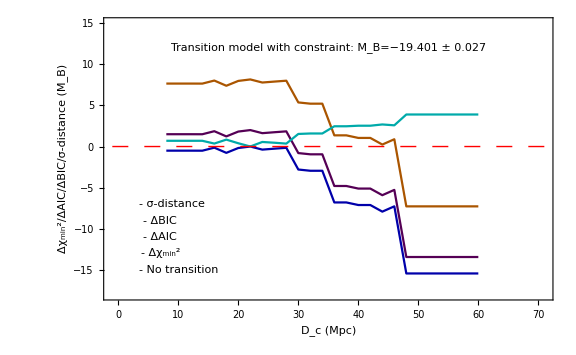

```mathematica
figsdmb=ListPlot[plsdist,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","σ-distance (M_B)"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{-0.5,6}},Axes->False,PlotStyle->{Darker[Cyan]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]];
figchimb=ListPlot[plchi2min,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","χ_min^2"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{3545,3570}},Axes->False,PlotStyle->{Darker[Cyan]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]];
figchiredmb=ListPlot[plchi2red,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","χ_red^2"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{1.0285,1.038}},Axes->False,PlotStyle->{Darker[Cyan]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]];
figaicmb=ListPlot[plaic,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","AIC"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{3642,3670}},Axes->False,PlotStyle->{Darker[Cyan]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]];
figdaicmb=ListPlot[pldaic,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","ΔAIC"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{-17,6}},Axes->False,PlotStyle->{Darker[Purple]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]];
figbicmb=ListPlot[plbic,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","BIC"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{3938,3970}},Axes->False,PlotStyle->{Darker[Cyan]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]];
figdbicmb=ListPlot[pldbic,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","ΔBIC"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{-12,12}},Axes->False,PlotStyle->{Darker[Orange]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]];
figdchi=ListPlot[pldchi,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","Δχ2"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{-20,4}},Axes->False,PlotStyle->{Darker[Blue]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]];
figmbcon=Show[figdchi,figdbicmb,figdaicmb,figsdmb,Graphics[{Inset[" Transition model with constraint: M_B=−19.401 ± 0.027",{35,12},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset[" - σ-distance",{9,-7},BaseStyle->{Italic,Bold,Darker[Cyan],FontFamily->"Times",12}]}],Graphics[{Inset[" - ΔBIC",{7,-9},BaseStyle->{Italic,Bold,Darker[Orange],FontFamily->"Times",12}]}],Graphics[{Inset[" - ΔAIC",{7,-11},BaseStyle->{Italic,Bold,Darker[Purple],FontFamily->"Times",12}]}],Graphics[{Inset[" - Δχ_min^2",{7,-13},BaseStyle->{Italic,Bold,Darker[Blue],FontFamily->"Times",12}]}],Graphics[{Inset[" - No transition ",{10,-15},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","Δχ_min^2/ΔAIC/ΔBIC/σ-distance (M_B)"},BaseStyle->{Large,FontFamily->"Times",16},LabelStyle->Directive[Black,FontFamily->"Times",18],PlotRange->{{-1,71},{-18,15}},Axes->False,PlotStyle->{Darker[Green]},Epilog->{Dashing[0.02],Red,Line[{{-1,0},{80,0}}]}, FrameStyle -> Directive[Black, Thick],ImageSize->Large]
Export[NotebookDirectory[]<>"figmbcon.pdf",figmbcon,ImageResolution->1000];
```